```mathematica
(* ============================================================ *)
(* Primordial Plots                                             *)
(* Dual-mass architecture: Vacuum and Fitted are explicit.      *)
(*                                                              *)
(* Required previous notebooks in the same kernel:              *)
(*   1. Intro_DualMass_VacuumFitted_Cugnon_v6_OriginalDirectKernels.wl *)
(*   2. PairFit_DualMass_MeVFit_RegisterFitted.wl               *)
(*   3. Distributions_DualMass_VacuumFitted_Cugnon_v5_OriginalDirectKernels.wl *)
(*   4. YieldTest_DualMass_VacuumFitted_Cugnon_v3.wl  optional  *)
(*                                                              *)
(* This notebook does not recompute spectra. It only plots      *)
(* tables created in Distributions.                             *)
(* ============================================================ *)

Print["========== Primordial Plots: dual-mass Vacuum/Fitted =========="];
```

========== Primordial Plots: dual-mass Vacuum/Fitted ==========

```mathematica
(* ------------------------------------------------------------ *)
(* 0. Minimal preflight checks                                  *)
(* ------------------------------------------------------------ *)

primordialRequiredSymbols = {
  "AllDistributionTablesByMode",
  "ProtonPlotData",
  "PionPPlotData",
  "PionMPlotData",
  "DeltaPPPlotData",
  "DeltaPPlotData",
  "Delta0PlotData",
  "DeltaMPlotData",
  "DeltaTotPlotData"
};

primordialMissingSymbols = Select[
   primordialRequiredSymbols,
   ! NameQ[#] &
];

If[Length[primordialMissingSymbols] > 0,
  Print[Style[
    "ERROR: Primordial Plots requires Distributions to be run first. Missing: " <>
      ToString[primordialMissingSymbols, InputForm],
    Red
  ]];
  Abort[];
];
```

```mathematica
(* ------------------------------------------------------------ *)
(* 1. Plot style conventions                                    *)
(* ------------------------------------------------------------ *)

ClearAll[primordialFiniteDataQ, primordialCleanData, primordialPlotStyle,
  primordialModeLabel, primordialMassLabel, primordialGet];

primordialFiniteDataQ[data_] :=
  ListQ[data] && Length[data] > 0 &&
   AllTrue[data, MatchQ[#, {_?NumericQ, _?NumericQ}] &];

primordialCleanData[data_] :=
  Select[data, MatchQ[#, {_?NumericQ, _?NumericQ}] && And @@ (NumericQ /@ #) &];

primordialPlotStyle[name_String] := Switch[name,
  "Proton", Blue,
  "PionPlus", Red,
  "PionMinus", Purple,
  "Delta++", Blue,
  "Delta+", Orange,
  "Delta0", Darker[Green],
  "Delta-", Purple,
  "DeltaTotal", Black,
  "Dirac", Black,
  "BreitWigner", Blue,
  "Cugnon", Orange,
  "PhaseShift", Darker[Green],
  "Vacuum", Dashed,
  "Fitted", Thick,
  _, Automatic
];

primordialModeLabel[mode_String] := Switch[mode,
  "Vacuum", "Vacuum",
  "Fitted", "Fitted",
  _, mode
];

primordialMassLabel[dist_String] := Switch[dist,
  "Dirac", "Dirac",
  "BreitWigner", "BW",
  "Cugnon", "Cugnon",
  "PhaseShift", "PS / Lo",
  _, dist
];

primordialGet[mode_String, component_String, dist_String, obj_String] := Module[{val},
  val = Quiet @ Check[AllDistributionTablesByMode[mode][component][dist][obj], $Failed];
  If[val === $Failed, {}, val]
];
```

```mathematica
(* ------------------------------------------------------------ *)
(* 2. Stable-particle primordial spectra                        *)
(* ------------------------------------------------------------ *)
(* Stable primordial proton and pion spectra do not depend on   *)
(* the Delta mass distribution. They are the same for Vacuum    *)
(* and Fitted. The proton table already contains the acceptance *)
(* factor exactly as in Distributions.                          *)
(* ------------------------------------------------------------ *)

PrimordialStableMtPlot = ListLogPlot[
  {
    primordialCleanData[ProtonPlotData],
    primordialCleanData[PionPPlotData],
    primordialCleanData[PionMPlotData]
  },
  Joined -> True,
  PlotRange -> All,
  Frame -> True,
  Axes -> False,
  FrameLabel -> {
    "m_t - m_0 [MeV]",
    "primordial spectrum"
  },
  PlotLegends -> {"p primordial", "pi+ primordial", "pi- primordial"},
  PlotStyle -> {Blue, Red, Purple},
  PlotLabel -> "Primordial stable-particle mT spectra",
  ImageSize -> Large
];

(* Rapidity spectra: linear axes, matching the original notebook. *)
If[NameQ["ProtonYPlotData"] && NameQ["PionPYPlotData"] && NameQ["PionMYPlotData"],
  PrimordialStableYPlot = ListPlot[
    {
      primordialCleanData[ProtonYPlotData],
      primordialCleanData[PionPYPlotData],
      primordialCleanData[PionMYPlotData]
    },
    Joined -> True,
    PlotRange -> All,
    Frame -> True,
    Axes -> False,
    FrameLabel -> {"y", "primordial dN/dy"},
    PlotLegends -> {"p primordial", "pi+ primordial", "pi- primordial"},
    PlotStyle -> {Blue, Red, Purple},
    PlotLabel -> "Primordial stable-particle rapidity spectra",
    ImageSize -> Large
  ],
  PrimordialStableYPlot = Style["Rapidity primordial tables not available.", Darker[Orange]]
];

(* Backward-compatible aliases used by older plotting notebooks. *)
PrimordialMtPlot = PrimordialStableMtPlot;
PrimordialYPlot = PrimordialStableYPlot;
```

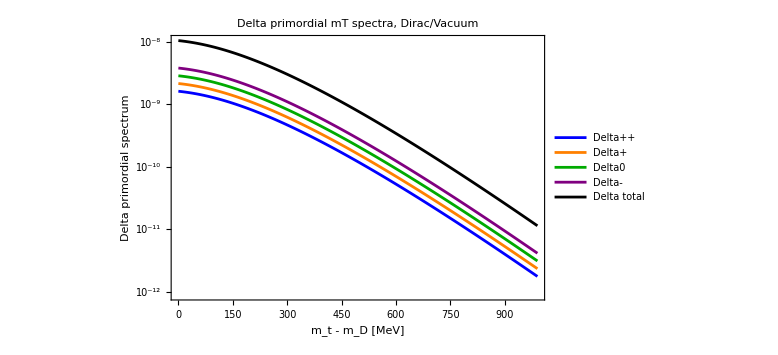

```mathematica
(* ------------------------------------------------------------ *)
(* 3. Delta primordial spectra: individual charge states        *)
(* ------------------------------------------------------------ *)

DeltaMtDiracVacuumPlot = ListLogPlot[
  {
    primordialCleanData[DeltaPPPlotData],
    primordialCleanData[DeltaPPlotData],
    primordialCleanData[Delta0PlotData],
    primordialCleanData[DeltaMPlotData],
    primordialCleanData[DeltaTotPlotData]
  },
  Joined -> True,
  PlotRange -> All,
  Frame -> True,
  Axes -> False,
  FrameLabel -> {"m_t - m_D [MeV]", "Delta primordial spectrum"},
  PlotLegends -> {"Delta++", "Delta+", "Delta0", "Delta-", "Delta total"},
  PlotStyle -> {Blue, Orange, Darker[Green], Purple, Black},
  PlotLabel -> "Delta primordial mT spectra, Dirac/Vacuum",
  ImageSize -> Large
];

DeltaMtPlot = DeltaMtDiracVacuumPlot
```

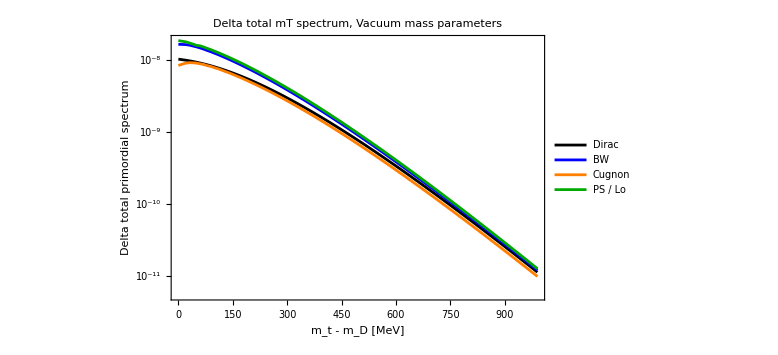

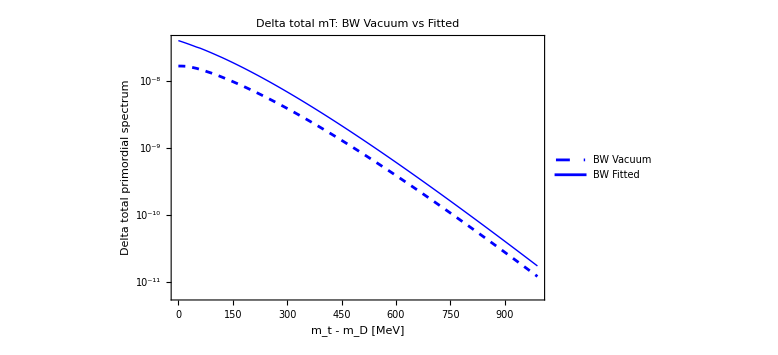

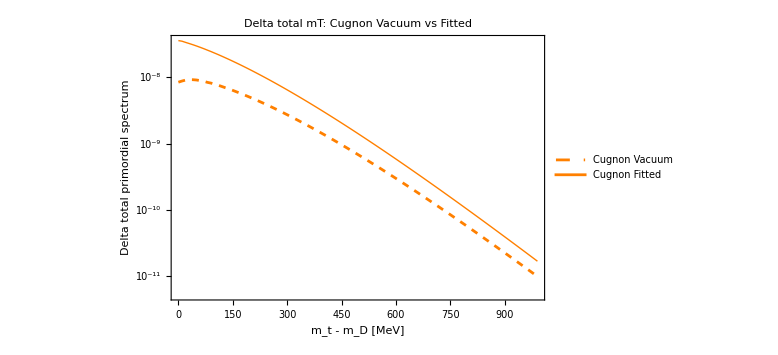

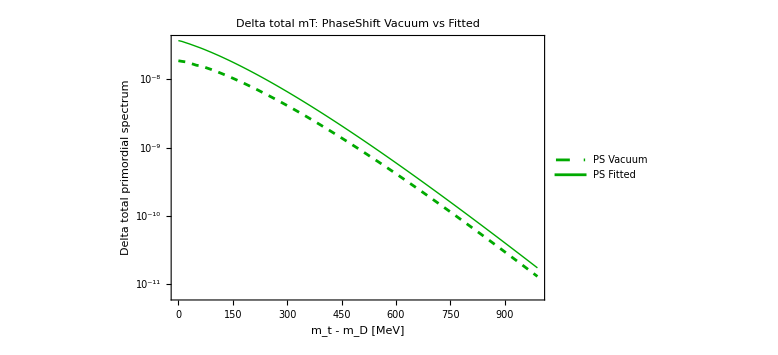

```mathematica
(* ------------------------------------------------------------ *)
(* 4. Delta total spectra by mass distribution and mode         *)
(* ------------------------------------------------------------ *)

ClearAll[deltaTotalMtData];

deltaTotalMtData[mode_String, dist_String] :=
  primordialCleanData @ primordialGet[mode, "DeltaMt", dist, "Total"];

DeltaMassTypeComparisonMtVacuumPlot = ListLogPlot[
  {
    deltaTotalMtData["Vacuum", "Dirac"],
    deltaTotalMtData["Vacuum", "BreitWigner"],
    deltaTotalMtData["Vacuum", "Cugnon"],
    deltaTotalMtData["Vacuum", "PhaseShift"]
  },
  Joined -> True,
  PlotRange -> All,
  Frame -> True,
  Axes -> False,
  FrameLabel -> {"m_t - m_D [MeV]", "Delta total primordial spectrum"},
  PlotLegends -> {"Dirac", "BW", "Cugnon", "PS / Lo"},
  PlotStyle -> {Black, Blue, Orange, Darker[Green]},
  PlotLabel -> "Delta total mT spectrum, Vacuum mass parameters",
  ImageSize -> Large
];

DeltaMassTypeComparisonMtFittedPlot = ListLogPlot[
  {
    deltaTotalMtData["Fitted", "Dirac"],
    deltaTotalMtData["Fitted", "BreitWigner"],
    deltaTotalMtData["Fitted", "Cugnon"],
    deltaTotalMtData["Fitted", "PhaseShift"]
  },
  Joined -> True,
  PlotRange -> All,
  Frame -> True,
  Axes -> False,
  FrameLabel -> {"m_t - m_D [MeV]", "Delta total primordial spectrum"},
  PlotLegends -> {"Dirac", "BW fitted", "Cugnon fitted", "PS / Lo fitted"},
  PlotStyle -> {Black, Blue, Orange, Darker[Green]},
  PlotLabel -> "Delta total mT spectrum, Fitted mass parameters",
  ImageSize -> Large
];

DeltaVacuumFittedBWMtPlot = ListLogPlot[
  {deltaTotalMtData["Vacuum", "BreitWigner"], deltaTotalMtData["Fitted", "BreitWigner"]},
  Joined -> True,
  PlotRange -> All,
  Frame -> True,
  Axes -> False,
  FrameLabel -> {"m_t - m_D [MeV]", "Delta total primordial spectrum"},
  PlotLegends -> {"BW Vacuum", "BW Fitted"},
  PlotStyle -> {Directive[Blue, Dashed], Directive[Blue, Thick]},
  PlotLabel -> "Delta total mT: BW Vacuum vs Fitted",
  ImageSize -> Large
];

DeltaVacuumFittedCugnonMtPlot = ListLogPlot[
  {deltaTotalMtData["Vacuum", "Cugnon"], deltaTotalMtData["Fitted", "Cugnon"]},
  Joined -> True,
  PlotRange -> All,
  Frame -> True,
  Axes -> False,
  FrameLabel -> {"m_t - m_D [MeV]", "Delta total primordial spectrum"},
  PlotLegends -> {"Cugnon Vacuum", "Cugnon Fitted"},
  PlotStyle -> {Directive[Orange, Dashed], Directive[Orange, Thick]},
  PlotLabel -> "Delta total mT: Cugnon Vacuum vs Fitted",
  ImageSize -> Large
];

DeltaVacuumFittedPSMtPlot = ListLogPlot[
  {deltaTotalMtData["Vacuum", "PhaseShift"], deltaTotalMtData["Fitted", "PhaseShift"]},
  Joined -> True,
  PlotRange -> All,
  Frame -> True,
  Axes -> False,
  FrameLabel -> {"m_t - m_D [MeV]", "Delta total primordial spectrum"},
  PlotLegends -> {"PS Vacuum", "PS Fitted"},
  PlotStyle -> {Directive[Darker[Green], Dashed], Directive[Darker[Green], Thick]},
  PlotLabel -> "Delta total mT: PhaseShift Vacuum vs Fitted",
  ImageSize -> Large
];

(* Backward-compatible aliases for common names. *)
DeltaMtBWPlot = DeltaMassTypeComparisonMtVacuumPlot
DeltaMtCugnonPlot = DeltaMassTypeComparisonMtVacuumPlot;
DeltaMtPSPlot = DeltaMassTypeComparisonMtVacuumPlot;
DeltaMtBWFittedPlot = DeltaVacuumFittedBWMtPlot
DeltaMtCugnonFittedPlot = DeltaVacuumFittedCugnonMtPlot
DeltaMtPSFittedPlot = DeltaVacuumFittedPSMtPlot
```

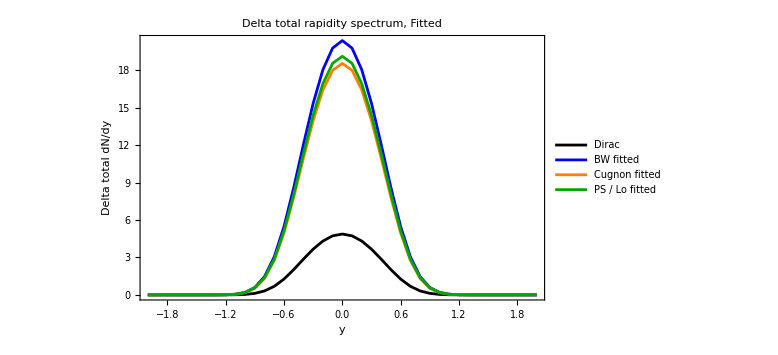

```mathematica
(* ------------------------------------------------------------ *)
(* 5. Rapidity versions, if tables are available                *)
(* As in the original Primordial Plots notebook, all rapidity  *)
(* spectra are drawn with linear axes using ListPlot. Only mT   *)
(* spectra use logarithmic vertical axes via ListLogPlot.       *)
(* ------------------------------------------------------------ *)

ClearAll[deltaTotalYData];

deltaTotalYData[mode_String, dist_String] :=
  primordialCleanData @ primordialGet[mode, "DeltaY", dist, "Total"];

If[primordialFiniteDataQ[deltaTotalYData["Vacuum", "Dirac"]],
  DeltaMassTypeComparisonYVacuumPlot = ListPlot[
    {
      deltaTotalYData["Vacuum", "Dirac"],
      deltaTotalYData["Vacuum", "BreitWigner"],
      deltaTotalYData["Vacuum", "Cugnon"],
      deltaTotalYData["Vacuum", "PhaseShift"]
    },
    Joined -> True,
    PlotRange -> All,
    Frame -> True,
    Axes -> False,
    FrameLabel -> {"y", "Delta total dN/dy"},
    PlotLegends -> {"Dirac", "BW", "Cugnon", "PS / Lo"},
    PlotStyle -> {Black, Blue, Orange, Darker[Green]},
    PlotLabel -> "Delta total rapidity spectrum, Vacuum",
    ImageSize -> Large
  ];

  DeltaMassTypeComparisonYFittedPlot = ListPlot[
    {
      deltaTotalYData["Fitted", "Dirac"],
      deltaTotalYData["Fitted", "BreitWigner"],
      deltaTotalYData["Fitted", "Cugnon"],
      deltaTotalYData["Fitted", "PhaseShift"]
    },
    Joined -> True,
    PlotRange -> All,
    Frame -> True,
    Axes -> False,
    FrameLabel -> {"y", "Delta total dN/dy"},
    PlotLegends -> {"Dirac", "BW fitted", "Cugnon fitted", "PS / Lo fitted"},
    PlotStyle -> {Black, Blue, Orange, Darker[Green]},
    PlotLabel -> "Delta total rapidity spectrum, Fitted",
    ImageSize -> Large
  ],
  DeltaMassTypeComparisonYVacuumPlot = Style["Delta rapidity tables not available.", Darker[Orange]];
  DeltaMassTypeComparisonYFittedPlot = Style["Delta rapidity tables not available.", Darker[Orange]];
]
```

```mathematica
(* ------------------------------------------------------------ *)
(* 6. Summary tables                                            *)
(* ------------------------------------------------------------ *)

ClearAll[primordialDataSummaryRow];

primordialDataSummaryRow[mode_String, dist_String, component_String, obj_String] := Module[
  {data = primordialCleanData @ primordialGet[mode, component, dist, obj]},
  If[Length[data] == 0,
    {mode, dist, component, obj, 0, Missing["NoData"], Missing["NoData"], Missing["NoData"], Missing["NoData"]},
    {mode, dist, component, obj, Length[data], Min[data[[All, 1]]], Max[data[[All, 1]]], Min[data[[All, 2]]], Max[data[[All, 2]]]}
  ]
];

primordialPlotSummaryTable = Grid[
  Prepend[
    Flatten[
      Table[
        primordialDataSummaryRow[mode, dist, "DeltaMt", "Total"],
        {mode, {"Vacuum", "Fitted"}},
        {dist, {"Dirac", "BreitWigner", "Cugnon", "PhaseShift"}}
      ],
      1
    ],
    {"Mode", "Mass distribution", "Component", "Object", "N", "xMin", "xMax", "yMin", "yMax"}
  ],
  Frame -> All,
  Background -> {None, {LightGray, None}}
];

Print["Primordial plot summary:"];
Print[primordialPlotSummaryTable];

Print["Primordial plots finished."];
```

Primordial plot summary:

Mode | Mass distribution | Component | Object | N | xMin | xMax | yMin | yMax
Vacuum | Dirac | DeltaMt | Total | 100 | 0.1 | 990.1 | 1.14603×10^-11 | 1.03847×10^-8
Vacuum | BreitWigner | DeltaMt | Total | 100 | 0.1 | 990.1 | 1.22256×10^-11 | 1.66743×10^-8
Vacuum | Cugnon | DeltaMt | Total | 100 | 0.1 | 990.1 | 9.998×10^-12 | 9.28007×10^-9
Vacuum | PhaseShift | DeltaMt | Total | 100 | 0.1 | 990.1 | 1.28276×10^-11 | 1.88184×10^-8
Fitted | Dirac | DeltaMt | Total | 100 | 0.1 | 990.1 | 1.14603×10^-11 | 1.03847×10^-8
Fitted | BreitWigner | DeltaMt | Total | 100 | 0.1 | 990.1 | 1.75134×10^-11 | 3.99239×10^-8
Fitted | Cugnon | DeltaMt | Total | 100 | 0.1 | 990.1 | 1.69642×10^-11 | 3.59601×10^-8
Fitted | PhaseShift | DeltaMt | Total | 100 | 0.1 | 990.1 | 1.71385×10^-11 | 3.72168×10^-8

Primordial plots finished.

```mathematica
(* ============================================================ *)
(* AUTOMATIC EXPORT                                              *)
(* ============================================================ *)

ClearAll[exportPrimordialPlots, plotExportObjectQ, plotExportDirectory];

plotExportObjectQ[obj_] := MatchQ[Head[obj], Graphics | Legended | Graphics3D];

plotExportDirectory[dir_String] := Module[{baseDir},
  baseDir = Quiet @ Check[NotebookDirectory[], Directory[]];
  If[!StringQ[baseDir], baseDir = Directory[]];
  FileNameJoin[{baseDir, dir}]
];

exportPrimordialPlots[dir_String:"PrimordialPlotsExport"] := Module[
  {targetDir, plots, exported},

  targetDir = plotExportDirectory[dir];

  If[!DirectoryQ[targetDir],
    CreateDirectory[targetDir, CreateIntermediateDirectories -> True]
  ];

  plots = <|
  "DeltaMassTypeComparisonMtFittedPlot.png" -> DeltaMassTypeComparisonMtFittedPlot,
  "DeltaMassTypeComparisonMtVacuumPlot.png" -> DeltaMassTypeComparisonMtVacuumPlot,
  "DeltaMassTypeComparisonYFittedPlot.png" -> DeltaMassTypeComparisonYFittedPlot,
  "DeltaMassTypeComparisonYVacuumPlot.png" -> DeltaMassTypeComparisonYVacuumPlot,
  "DeltaMtBWFittedPlot.png" -> DeltaMtBWFittedPlot,
  "DeltaMtBWPlot.png" -> DeltaMtBWPlot,
  "DeltaMtCugnonFittedPlot.png" -> DeltaMtCugnonFittedPlot,
  "DeltaMtCugnonPlot.png" -> DeltaMtCugnonPlot,
  "DeltaMtDiracVacuumPlot.png" -> DeltaMtDiracVacuumPlot,
  "DeltaMtPSFittedPlot.png" -> DeltaMtPSFittedPlot,
  "DeltaMtPSPlot.png" -> DeltaMtPSPlot,
  "DeltaMtPlot.png" -> DeltaMtPlot,
  "DeltaVacuumFittedBWMtPlot.png" -> DeltaVacuumFittedBWMtPlot,
  "DeltaVacuumFittedCugnonMtPlot.png" -> DeltaVacuumFittedCugnonMtPlot,
  "DeltaVacuumFittedPSMtPlot.png" -> DeltaVacuumFittedPSMtPlot,
  "PrimordialMtPlot.png" -> PrimordialMtPlot,
  "PrimordialStableMtPlot.png" -> PrimordialStableMtPlot,
  "PrimordialStableYPlot.png" -> PrimordialStableYPlot,
  "PrimordialYPlot.png" -> PrimordialYPlot
  |>;

  exported = KeyValueMap[
    Function[{file, plot},
      If[plotExportObjectQ[plot],
        Export[FileNameJoin[{targetDir, file}], plot];
        FileNameJoin[{targetDir, file}],
        Nothing
      ]
    ],
    plots
  ];

  Print["Exported ", Length[exported], " plot files to: ", targetDir];
  exported
];

exportPrimordialPlots[];
```

Exported 19 plot files to: C:\Users\nikko\Desktop\Coalescence\Delta With Fit\PrimordialPlotsExport